## Slope of FSSD

Will assume Gaussian p,q and a Gaussian kernel.

```mathematica
Subscript[μ, p]=0
Subscript[σ, p]=1
logp[x_]:=-(x-Subscript[μ, p])^2/(2*Subscript[σ, p]^2)
ker[x_,y_,s_]:=Exp[-(x-y)^2/(2*s)]
Dkx[x_,y_,s_]:=D[ker[x,y,s],x]
Dky[x_,y_,s_]:=D[ker[x,y,s],y]
Dkxy[x_,y_,s_]:=D[Dkx[x,y,s],y]
```

0

1

```mathematica
xi[x_,v_]:=logp'[x]*ker[x,v,Subscript[σ, k]^2]+Dkx[x,v,Subscript[σ, k]^2]
```

```mathematica
xi[x,v]
```

-ⅇ^(-(-v+x)^2/(2 σ_k^2)) x-(ⅇ^(-(-v+x)^2/(2 σ_k^2)) (-v+x))/σ_k^2

```mathematica
exi=Expectation[xi[x,v],x\[Distributed]NormalDistribution[Subscript[μ, q],Subscript[σ, q]]]
```

-(ⅇ^(-(v-μ_q)^2/(2 (σ_k^2+σ_q^2))) (μ_q (1+σ_k^2)+v (-1+σ_q^2)))/(√(1/σ_k^2+1/σ_q^2) σ_q (σ_k^2+σ_q^2))

```mathematica
Simplify[exi/.{Subscript[μ, q]->0}]
```

-(ⅇ^(-v^2/(2 (σ_k^2+σ_q^2))) v (-1+σ_q^2))/(√(1/σ_k^2+1/σ_q^2) σ_q (σ_k^2+σ_q^2))

```mathematica
Simplify[exi/.{Subscript[σ, q]->1}]
```

-(ⅇ^(-(v-μ_q)^2/(2 (1+σ_k^2))) μ_q)/(√(1+1/σ_k^2))

```mathematica
fssd2=Simplify[exi^2]
```

(ⅇ^(-(v-μ_q)^2/(σ_k^2+σ_q^2)) σ_k^2 (μ_q (1+σ_k^2)+v (-1+σ_q^2))^2)/((σ_k^2+σ_q^2)^3)

```mathematica
exi2 = Assuming[Subscript[σ, k]>0,Expectation[xi[x,v]^2,x\[Distributed]NormalDistribution[Subscript[μ, p],Subscript[σ, p]]]]
```

(ⅇ^(-v^2/(2+σ_k^2)) (2+(5+v^2) σ_k^2+4 σ_k^4+σ_k^6))/(σ_k (2+σ_k^2)^(5/2))

```mathematica
vxip = Simplify[exi2]
```

(ⅇ^(-v^2/(2+σ_k^2)) (2+(5+v^2) σ_k^2+4 σ_k^4+σ_k^6))/(σ_k (2+σ_k^2)^(5/2))

```mathematica
f$vxip[v1_,sq1_,sk1_]:=vxip/.{v->v1,Subscript[σ, q]->Sqrt[sq1],Subscript[σ, k]->Sqrt[sk1]}
```

```mathematica
e2xi=Assuming[Subscript[σ, k]>0,exi^2]//Simplify
```

(ⅇ^(-(v-μ_q)^2/(σ_k^2+σ_q^2)) σ_k^2 (μ_q (1+σ_k^2)+v (-1+σ_q^2))^2)/((σ_k^2+σ_q^2)^3)

```mathematica
slope$fssd = (e2xi/vxip)
```

(ⅇ^(v^2/(2+σ_k^2)-(v-μ_q)^2/(σ_k^2+σ_q^2)) σ_k^3 (2+σ_k^2)^(5/2) (μ_q (1+σ_k^2)+v (-1+σ_q^2))^2)/((2+(5+v^2) σ_k^2+4 σ_k^4+σ_k^6) (σ_k^2+σ_q^2)^3)

```mathematica
f$slope$fssd[v1_,mq1_,sq1_,sk1_]:=slope$fssd/.{v->v1,Subscript[μ, q]->mq1,Subscript[σ, q]->Sqrt[sq1],Subscript[σ, k]->Sqrt[sk1]}
```

```mathematica
f$slope$fssd[v,Subscript[μ, q],Subscript[σ, q]^2,Subscript[σ, k]^2] // Simplify
```

(ⅇ^(v^2/(2+σ_k^2)-(v-μ_q)^2/(σ_k^2+σ_q^2)) (σ_k^2)^(3/2) (2+σ_k^2)^(5/2) (μ_q (1+σ_k^2)+v (-1+σ_q^2))^2)/((2+(5+v^2) σ_k^2+4 σ_k^4+σ_k^6) (σ_k^2+σ_q^2)^3)

```mathematica
f$slope$fssd[v,0,Subscript[σ, q]^2,Subscript[σ, k]^2]
```

(ⅇ^(v^2/(2+σ_k^2)-v^2/(σ_k^2+σ_q^2)) v^2 (σ_k^2)^(3/2) (2+σ_k^2)^(5/2) (-1+σ_q^2)^2)/((2+(5+v^2) σ_k^2+4 σ_k^4+σ_k^6) (σ_k^2+σ_q^2)^3)

```mathematica
f$slope$fssd[v,Subscript[μ, q],1,Subscript[σ, k]^2]
```

(ⅇ^(-(v-μ_q)^2/(1+σ_k^2)+v^2/(2+σ_k^2)) μ_q^2 (σ_k^2)^(3/2) (2+σ_k^2)^(5/2))/((1+σ_k^2) (2+(5+v^2) σ_k^2+4 σ_k^4+σ_k^6))

Ratio of two Gaussian densities

```mathematica
r[x_,mr_,sr_]:=Exp[-(x-mr)^2/(2*sr)];
s[x_,ms_,ss_]:=Exp[-(x-ms)^2/(2*ss)]
```

```mathematica
r[x,0,sr]/s[x,0, 1]
```

ⅇ^(x^2/2-x^2/(2 sr))

```mathematica
Manipulate[Plot[r[x,0,sr]/s[x,0, 1], {x, -10, 10}], {{sr, 0.1}, 0.1, 5,0.1}]
```

## Zero-mean Gaussian case

```mathematica
f$slope$fssd$mq0[v1_,sq1_,sk1_]:=f$slope$fssd[v1,0,sq1,sk1]
```

```mathematica
f$slope$fssd$mq0[v,Subscript[σ, q]^2,Subscript[σ, k]^2]//Simplify
```

(ⅇ^(v^2 (1/(2+σ_k^2)-1/(σ_k^2+σ_q^2))) v^2 (σ_k^2)^(3/2) (2+σ_k^2)^(5/2) (-1+σ_q^2)^2)/((2+(5+v^2) σ_k^2+4 σ_k^4+σ_k^6) (σ_k^2+σ_q^2)^3)

```mathematica
f$slope$fssd$mq0[Subscript[σ, q],Subscript[σ, q]^2,Subscript[σ, q]^2]//Simplify
```

(ⅇ^(-1/2+σ_q^2/(2+σ_q^2)) (-1+σ_q^2)^2 (2+σ_q^2)^(5/2))/(8 √(σ_q^2) (2+5 σ_q^2+5 σ_q^4+σ_q^6))

```mathematica
f$slope$fssd$mq0[v,Subscript[σ, q]^2,1]//Simplify
```

(9 √3 ⅇ^(1/3 v^2 (1-3/(1+σ_q^2))) v^2 (-1+σ_q^2)^2)/((12+v^2) (1+σ_q^2)^3)

```mathematica
f$slope$fssd$mq0[Subscript[σ, q]+1,Subscript[σ, q]^2,Boole[Subscript[σ, q]<1] Subscript[σ, q]^2+Boole[Subscript[σ, q]≥ 1] ]//Simplify
```

Piecewise[{{(9 √3 ⅇ^(((1+σ_q)^2 (-2+σ_q^2))/(3 (1+σ_q^2))) (-1+σ_q)^2 (1+σ_q)^4)/((1+σ_q^2)^3 (13+2 σ_q+σ_q^2)), σ_q≥1}, {(ⅇ^(((1+σ_q)^2 (-2+σ_q^2))/(2 σ_q^2 (2+σ_q^2))) (-1+σ_q)^2 √(σ_q^2) (1+σ_q)^4 (2+σ_q^2)^(5/2))/(8 σ_q^4 (2+6 σ_q^2+2 σ_q^3+5 σ_q^4+σ_q^6)), True}}]

```mathematica
Manipulate[Plot3D[f$slope$fssd$mq0[v,sq^2,sk^2],{v,0.01,3},{sk,0.01,3},AxesLabel->Automatic],{sq,0.01,3}]
```

```mathematica
Manipulate[NMaximize[f$slope$fssd$mq0[v,sq^2,sk^2],{v,sk}],{sq,0.01,3}]
```

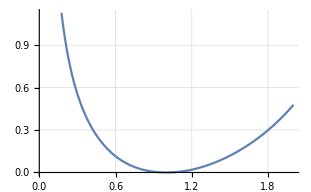

```mathematica
Plot[f$slope$fssd$mq0[Subscript[σ, q],Subscript[σ, q]^2,Boole[Subscript[σ, q]<1] Subscript[σ, q]^2+Boole[Subscript[σ, q]≥ 1] ],{Subscript[σ, q],0,2},GridLines->Automatic]
```

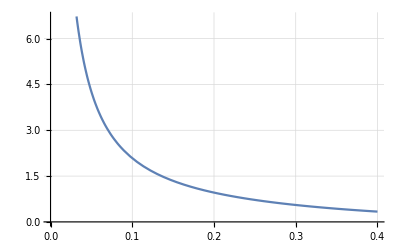

```mathematica
Plot[f$slope$fssd$mq0[Subscript[σ, q],Subscript[σ, q]^2,Subscript[σ, q]^2],{Subscript[σ, q],0,0.4},GridLines->Automatic]
```

```mathematica
f$vxip[v,Subscript[σ, q]^2,Subscript[σ, k]^2]
```

(ⅇ^(-v^2/(2+σ_k^2)) √(1+2/σ_k^2) (2+(5+v^2) σ_k^2+4 σ_k^4+σ_k^6))/((2+σ_k^2)^3)

```mathematica
Manipulate[Plot3D[f$vxip[v,sq^2,sk^2],{v,0.01,5},{sk,0.01,5},AxesLabel->Automatic],{sq,0.01,5}]
```

```mathematica
f$slope$fssd$mq0[v,Subscript[σ, q]^2,Subscript[σ, k]^2]/f$slope$lkstein$mq0[Subscript[σ, q]^2,κ^2]
```

(ⅇ^(v^2/(2+σ_k^2)-v^2/(σ_k^2+σ_q^2)) v^2 σ_k^2 (2+σ_k^2)^3 (-1+σ_q^2)^2)/(f$slope$lkstein$mq0[σ_q^2,κ^2] √(1+2/σ_k^2) (2+(5+v^2) σ_k^2+4 σ_k^4+σ_k^6) (σ_k^2+σ_q^2)^3)

## Best parameters in the unit-variance case

```mathematica
f$slope$fssd$sq1[v1_,mq1_,sk1_]:=f$slope$fssd[v1,mq1,1,sk1]
```

```mathematica
f$slope$fssd$sq1[v,Subscript[μ, q],Subscript[σ, k]^2]//Simplify
```

(ⅇ^(-(v-μ_q)^2/(1+σ_k^2)+v^2/(2+σ_k^2)) μ_q^2 σ_k^2 (2+σ_k^2)^3)/(√(1+2/σ_k^2) (1+σ_k^2) (2+(5+v^2) σ_k^2+4 σ_k^4+σ_k^6))

```mathematica
f$slope$fssd$sq1[Subscript[μ, q],Subscript[μ, q],Subscript[σ, k]^2]
```

(ⅇ^(μ_q^2/(2+σ_k^2)) μ_q^2 σ_k^2 (2+σ_k^2)^3)/(√(1+2/σ_k^2) (1+σ_k^2) (2+(5+μ_q^2) σ_k^2+4 σ_k^4+σ_k^6))

```mathematica
f$slope$fssd$sq1[Subscript[μ, q],Subscript[μ, q],1]
```

(9 √3 ⅇ^(μ_q^2/3) μ_q^2)/(2 (12+μ_q^2))

```mathematica
Reduce[f$slope$fssd$sq1[Subscript[μ, q],Subscript[μ, q],1]>slope$lkstein$sq1$lim]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[(9 √3 ⅇ^(μ_q^2/3) μ_q^2)/(2 (12+μ_q^2))>slope$lkstein$sq1$lim]

```mathematica
f$slope$fssd$sq1[Subscript[μ, q],Subscript[μ, q],1]/slope$lkstein$sq1$lim //Simplify
```

(9 √3 ⅇ^(μ_q^2/3) μ_q^2)/(24 slope$lkstein$sq1$lim+2 slope$lkstein$sq1$lim μ_q^2)

```mathematica
f$slope$fssd$sq1[Subscript[μ, q],Subscript[μ, q],1]-slope$lkstein$sq1$lim
```

-slope$lkstein$sq1$lim+(9 √3 ⅇ^(μ_q^2/3) μ_q^2)/(2 (12+μ_q^2))

```mathematica
(9 √3 ⅇ^(Subscript[μ, q]^2/3) Subscript[μ, q]^2)/(2 (12+Subscript[μ, q]^2))-Subscript[μ, q]^4/(2+4 Subscript[μ, q]^2)
```

(9 √3 ⅇ^(μ_q^2/3) μ_q^2)/(2 (12+μ_q^2))-μ_q^4/(2+4 μ_q^2)

```mathematica
Plot3D[f$slope$fssd$sq1[Subscript[μ, q],Subscript[μ, q],Subscript[σ, k]^2],{Subscript[μ, q],0.001,2},{Subscript[σ, k],0.001,20},AxesLabel->Automatic]
```

-Graphics3D-